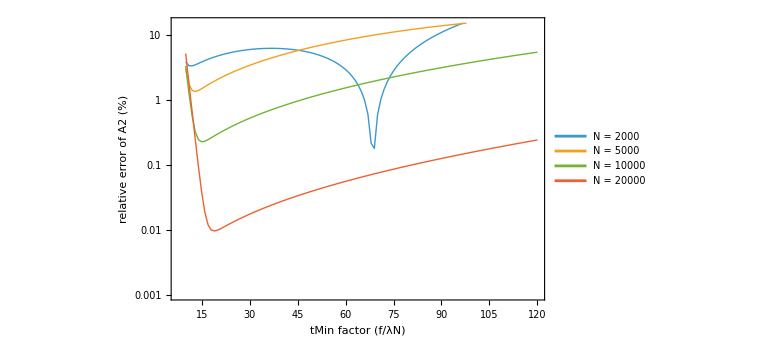

C:/Users/sulta/git/cone-operator-lab/plots/plotA2ErrorMin.pdf

```mathematica
ClearAll["Global`*"];

path="C:/Users/sulta/git/cone-operator-lab/data/eigenvalues/box_a1.0_b1.5_c2.3_N20000.txt";
allEigs=Sort@Select[Flatten@Import[path,"Table"]//N,#>0&];
A2true=(1.0+1.5+2.3)/(4 Pi^2);

(*Wir scannen für verschiedene N-Stufen*)
nSteps={2000,5000,10000,20000};
factors=Range[10,120,1];

plots=Table[eigs=allEigs[[1;;n]];
λN=Last[eigs];
errs=Table[tMin=f/λN;tMax=500/λN;
tGrid=Exp@Subdivide[Log[tMin],Log[tMax],250];
Z=Total[Exp[-Outer[Times,eigs,tGrid]],{1}];
X=Table[t^{-3/2,-1,-1/2,0},{t,tGrid}];
coef=PseudoInverse[X].Z;
A2hat=(coef[[3]]*(4 Pi)^(3/2))/(4 Pi^3);
Abs[A2hat/A2true-1]*100,{f,factors}];
Transpose[{factors,errs}],{n,nSteps}];

plotA2ErrorMin=ListLogPlot[plots,
Joined->True,
PlotRange->{All,{0.001,15}},
PlotStyle->Thick,
PlotLegends->Placed[StringTemplate["N = ``"]/@nSteps,Above],
Frame->True,
FrameLabel->{"tMin factor (f/λN)","relative error of A2 (%)"},
FrameTicks->{Automatic,All},
GridLines->None,
ImageSize->Large]
Export["C:/Users/sulta/git/cone-operator-lab/plots/plotA2ErrorMin.pdf",
plotA2ErrorMin,
"PDF",
ImageResolution->300
]
```